```mathematica
num=200;
hbar=1;
range=20;(*Distance in fm*)
δx=range/num//N;
δk=(2π)/(num δx)//N;
space=Table[(j-(num/2))*δx,{j,1,num}];
kspace=Table[(j-(num/2))*δk,{j,1,num}];
absk=Table[kspace[[j]]+k0,{j,1,num}];
```

```mathematica
(*Deleting the value of 0 from our space array to stop it from trying to evaluate 1/0*)
space[[num/2]]=.02;
```

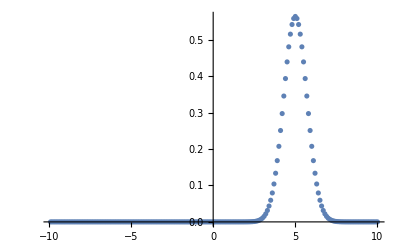

```mathematica
(*Defining the wavefunction that we are using*)
μ=1;
a0=.5;
a=1;
V0=50;(*MeV*)
x0=5;
σ0=1;
k0=10;
n=(1/π)^(1/4);(*Only the case for the above conditions*)
x=.;
ψ[x_]:=n Exp[-((x-x0)^2)/(2σ0^2)]*Exp[-I k0 (x)];
ψ0=Table[ψ[space[[j]]],{j,1,num}];
ListPlot[Table[{space[[j]],ψ0[[j]]*Conjugate[ψ0[[j]]]},{j,1,num}],PlotRange->All]
```

```mathematica
x=.;
t=.;
q1=1; (*Charge on the incoming particle*)
q2=1;(*Charge on the stationary nuclei*)
ϵ0=1; (*Permitivity of free space*)
dt=.012;
delta= .1;
J=Length[space]-1;
dx=space[[2]]-space[[1]];
Hmax=0+1/dx^2;
τ=Hmax dt;
ii=2;
Jnτ=Table[2*(-I )^(j)BesselJ[j,τ],{j,0,13}];
Npoly=Length[Jnτ];
```

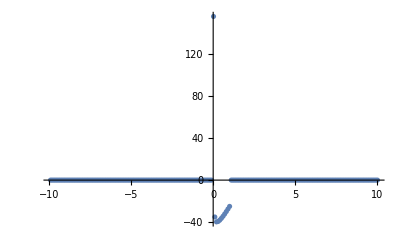

```mathematica
(*Defining the Kinetic and potential energies respectively*)
Hmax=0+(1/(dx^2));
(*We need to make it so that we have a piecewise version of this matrix for the different values of space, so for the situation were 0<=x<=a*)
V[x_]:=-V0/(1+Exp[(x-a)/a0])+(q1 q2)/(4π ϵ0 x^2)
potential=DiagonalMatrix[Table[0,{j,1,num}]];
For[j=1,j<=num,j++,
If[0<=space[[j]]<=a,
potential[[j,j]]=V[space[[j]]];
]];
kinetic=-(1/(2 dx^2))*(DiagonalMatrix[Table[-2,{j,1,num}]]+DiagonalMatrix[Table[1,{j,1,num-1}],1]+DiagonalMatrix[Table[1,{j,1,num-1}],-1]);
H=(kinetic+potential)/Hmax;
ListPlot[Table[{space[[j]],potential[[j,j]]},{j,1,num}]]
```

```mathematica
ψt=Table[Table[0,{j,1,num}],{n,1,J+1}];
ψshebyexp=Table[Table[0,{j,1,Npoly}],{n,1,J+1}];
ψt[[;;,1]]=ψ0;
ψshebyexp[[;;,1]]=ψ0;
(*Notably we have J+1 rows and NPoly columns here*)
```

```mathematica
m=num;
For[n=1,n<m,n++,
ψshebyexp[[;;,1]]=ψt[[;;,n]];
ψshebyexp[[;;,2]]=H.(ψshebyexp[[;;,1]]);
For[jj=3, jj<Npoly,jj++,
ψshebyexp[[;;,jj]]=2 H.ψshebyexp[[;;,jj-1]];
ψshebyexp[[;;,jj]]=ψshebyexp[[;;,jj]]-ψshebyexp[[;;,jj-2]]];
ψt[[;;,n+1]]=ψshebyexp.Jnτ]
```

```mathematica
(*Now we normalize all of our results of ψt*)
For[ib=1,ib<num,ib++,
norm=.;
norm=1/(Sqrt[Sum[ψt[[j,ib]]Conjugate[ψt[[j,ib]]],{j,1,num}]]);
 ψt[[;;,ib]]=ψt[[;;,ib]] norm;]
```

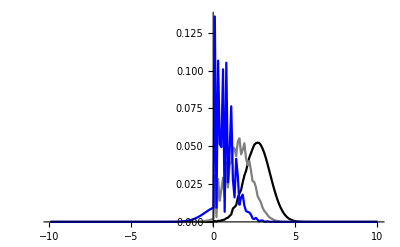

```mathematica
j=.;
ListPlot[{Table[{space[[j]],ψt[[j,40]]Conjugate[ψt[[j,40]]]},{j,1,num}],Table[{space[[j]],ψt[[j,60]]Conjugate[ψt[[j,60]]]},{j,1,num}],Table[{space[[j]],ψt[[j,80]]Conjugate[ψt[[j,80]]]},{j,1,num}]},PlotRange->All,Joined->True,PlotStyle->{Black,Gray,Blue}]
```

```mathematica
(*Now we look to animate this function to see the propogation of these functions*)Export["Coloumb Barrier with a woodsxon large range 50MevWell.avi",Animate[ListPlot[{Table[{space[[j]],500ψt[[j,b]] Conjugate[ψt[[j,b]]]},{j,1,num}],Table[{space[[j]],potential[[j,j]]},{j,1,num}]},PlotRange->{{-10,10},{-50,50}},Joined->True],{b,1,num,1}]]
```

Coloumb Barrier with a woodsxon large range 50MevWell.avi

```mathematica
(*These are just the Chebyshev polynomials, so now we need to incorporate the time dependence.*)
Ψ[t_]:=ψt*Exp[-I Hmax t/(2hbar)]
Ψ[t=1][[30,1]]Conjugate[Ψ[t=1][[30,1]]]
Ψ[t=100][[30,1]]Conjugate[Ψ[t=100][[30,1]]]
```

1.63313×10^-64+0. ⅈ

1.63313×10^-64+0. ⅈ

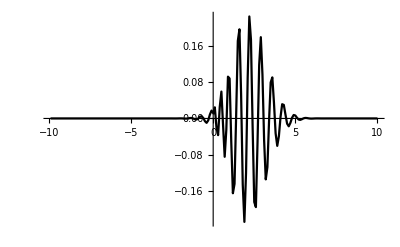

```mathematica
t=1;
ListPlot[{Table[{space[[j]],Re[Ψ[t=3][[j,50]] ]},{j,1,num}]  },PlotRange->All,PlotLegends->Automatic,PlotStyle->{Black,Red,Yellow,Blue,Orange},Joined->True]
```

```mathematica
(*Now we check for the conservation of mean energy.*)
Conjugate[ψt[[;;,10]]].H. ψt[[;;,10]]
Conjugate[ψt[[;;,20]]].H. ψt[[;;,20]]
Conjugate[ψt[[;;,30]]].H. ψt[[;;,30]]
Conjugate[ψt[[;;,40]]].H. ψt[[;;,40]]
```

0.450936+0. ⅈ

0.440476-9.54098×10^-18 ⅈ

0.430736+2.60209×10^-18 ⅈ

0.421634-1.21431×10^-17 ⅈ

```mathematica
(*This is essentially constant here so we have conserved mean energy in time as well!*)
ListPlot[Table[{0+dt*j,Conjugate[ψt[[;;,j]]].H. ψt[[;;,j]]},{j,1,num}],Frame->True,FrameLabel->{"Time","Mean Energy (Mev)"}]
```

-Graphics-

```mathematica
(*Now we check for the conservation of norm here*)
Sum[Conjugate[ψt[[j,10]]] ψt[[j,10]],{j,1,num}]
Sum[Conjugate[ψt[[j,20]]] ψt[[j,20]],{j,1,num}]
Sum[Conjugate[ψt[[j,30]]] ψt[[j,30]],{j,1,num}]
Sum[Conjugate[ψt[[j,40]]]ψt[[j,40]],{j,1,num}]

ListPlot[Table[{0+dt*j,Conjugate[ψt[[;;,j]]]. ψt[[;;,j]]},{j,1,num}],Frame->True,FrameLabel->{"Time","Norm"},PlotRange->{{0,2},{0,2}}]
```

1.+0. ⅈ

1.+0. ⅈ

1.+0. ⅈ

«1 more identical outputs»

-Graphics-